1000000

| Estimate | Standard Error | t-Statistic | P-Value
Ref | 7.82157×10^62 | 3.79839×10^77 | 2.05918×10^-15 | 1

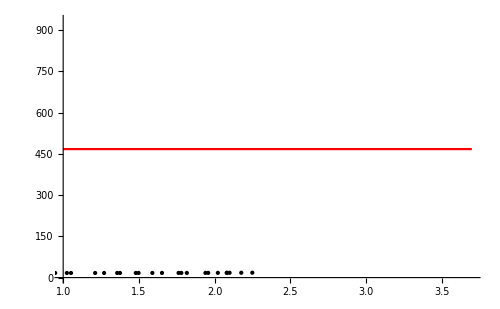

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola.dat"];
L=Length[data];
Ie=1000000
(*Ref = 12*)
Ip[R_]:=Ie*Exp[-7.669*((R/Ref)^0.25-1.0)]
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Ip[R],{Ref},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,1,3.7},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```